## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGMd";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_PGMd_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

((2pg)^c⇌(3pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 2.9815 | 2.83242
3.13057 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | Null | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | Null | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌(3pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 2.9815 | 2.83242
3.13057 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | Null | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | Null | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[(3pg)^c⇌(2pg)^c, PGMd]
```

((3pg)^c⇌(2pg)^c)^PGMd

```mathematica
catalyticBranch={"E_PGMd[c] + 2pg[c] <=> E_PGMd[c]&2pg",

				"E_PGMd[c]&2pg <=> E_PGMd[c]&3pg",
				
				"E_PGMd[c]&3pg <=> E_PGMd[c] + 3pg[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGMd^c)_^+(2pg)^c⇌(PGMd^c&(2pg)^c)_^)^PGMd1,((PGMd^c&(3pg)^c)_^⇌(PGMd^c)_^+(3pg)^c)^PGMd2,((PGMd^c&(2pg)^c)_^⇌(PGMd^c&(3pg)^c)_^)^PGMd3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMd^c)_^+(2pg)^c⇌(PGMd^c&(2pg)^c)_^)^PGMd1,Overscript[(PGMd^c&(3pg)^c)_^⇌(PGMd^c)_^+(3pg)^c, PGMd2],((PGMd^c&(2pg)^c)_^⇌(PGMd^c&(3pg)^c)_^)^PGMd3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGMd^c&(2pg)^c)_^-((PGMd^c&(3pg)^c)_^)/K_PGMd3) Volume_c k_PGMd3^⟶}

Volume_c (-(PGMd^c&(3pg)^c)_^ k_PGMd3^⟵+(PGMd^c&(2pg)^c)_^ k_PGMd3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
flux = 0.0012546434607581675;
FluxExpression = absoluteFlux /. {metabolite["2pg", "c"] -> 0.000149989144013334,metabolite["3pg","c"]-> 0,
     parameter["PGMd_total"] -> 0.00000318901651857926, parameter["Volume", "c"] -> 1};  (*Do I make the flux negative? It gives me an error if I do so?*)
```

```mathematica
FluxExpression2 = parameter["v", "PGMd"] /. FluxExpression;
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	3pg[c]	param_PGMd_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt"	2.98149708
1	0	0.00002	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.09090909090909091
1	0	0.00003169786384922229	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.13680688860321008
1	0	0.00005023772863019165	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.2007600089131019
1	0	0.00007962143411069939	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.2847472489508013
1	0	0.0001261914688960386	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.38686317984685686
1	0	0.00020000000000000004	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.5
1	0	0.0003169786384922229	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.6131368201531432
1	0	0.0005023772863019165	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.7152527510491988
1	0	0.0007962143411069948	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.7992399910868982
1	0	0.0012619146889603862	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.8631931113967899
1	0	0.0020000000000000005	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt"	0.9090909090909091
1	0.000018999999999999994	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.09090909090909087
1	0.00003011297065676116	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.13680688860321003
1	0.00004772584219868205	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.0000756403624051644	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.2847472489508012
1	0.00011988189545123664	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.38686317984685686
1	0.00018999999999999996	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.49999999999999994
1	0.0003011297065676116	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0004772584219868205	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.7152527510491987
1	0.0007564036240516448	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.0011988189545123664	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.0018999999999999996	0	1	7	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt"	0.9090909090909092
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt"	626.7176791692085
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt"	417.8117861128057
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675
3	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt"	0.0012546434607581675

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateFor_2pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/relRateRev_3pg.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGMd_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.07561618782
best_fit: 1.05031454942
best_fit: 1.09983261886
best_fit: 0.951526829448
best_fit: 0.965447716699
best_fit: 1.09716026166
best_fit: 1.09824786413
best_fit: 0.82954168603
best_fit: 1.0588277941
best_fit: 1.02785015678

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | haldaneRatio_1 | 0.0286472 | 0.00082066 | 0.190321 | 6.3834 | 2.9815 | 2.79118
1 | relRateRev_3pg | 0.0740114 | 0.00547768 | 0.0142443 | 15.6687 | 0.0909091 | 0.0766648
1 | relRateRev_3pg | 0.0705576 | 0.00497838 | 0.0205147 | 14.9954 | 0.136807 | 0.116292
1 | relRateRev_3pg | 0.0656989 | 0.00431635 | 0.0281849 | 14.0391 | 0.20076 | 0.172575
1 | relRateRev_3pg | 0.0592346 | 0.00350873 | 0.0363053 | 12.75 | 0.284747 | 0.248442
1 | relRateRev_3pg | 0.051243 | 0.00262584 | 0.0430564 | 11.1296 | 0.386863 | 0.343807
1 | relRateRev_3pg | 0.0422137 | 0.001782 | 0.046313 | 9.26261 | 0.5 | 0.453687
1 | relRateRev_3pg | 0.0329927 | 0.00108852 | 0.0448538 | 7.31546 | 0.613137 | 0.568283
1 | relRateRev_3pg | 0.0244984 | 0.000600174 | 0.0392303 | 5.48482 | 0.715253 | 0.676022
1 | relRateRev_3pg | 0.0173855 | 0.000302255 | 0.0313629 | 3.92409 | 0.79924 | 0.767877
1 | relRateRev_3pg | 0.01189 | 0.000141372 | 0.0233117 | 2.70063 | 0.863193 | 0.839881
1 | relRateRev_3pg | 0.00790269 | 0.0000624525 | 0.0163928 | 1.80321 | 0.909091 | 0.892698
1 | relRateFor_2pg | 0.28597 | 0.0817789 | 0.0847123 | 93.1835 | 0.0909091 | 0.175621
1 | relRateFor_2pg | 0.266008 | 0.0707602 | 0.115609 | 84.5049 | 0.136807 | 0.252415
1 | relRateFor_2pg | 0.239639 | 0.0574271 | 0.147831 | 73.6359 | 0.20076 | 0.348591
1 | relRateFor_2pg | 0.207277 | 0.0429639 | 0.174173 | 61.1674 | 0.284747 | 0.45892
1 | relRateFor_2pg | 0.170925 | 0.0292153 | 0.186569 | 48.2262 | 0.386863 | 0.573432
1 | relRateFor_2pg | 0.133912 | 0.0179323 | 0.180584 | 36.1168 | 0.5 | 0.680584
1 | relRateFor_2pg | 0.0998067 | 0.00996139 | 0.158413 | 25.8365 | 0.613137 | 0.77155
1 | relRateFor_2pg | 0.0711671 | 0.00506476 | 0.127357 | 17.8059 | 0.715253 | 0.84261
1 | relRateFor_2pg | 0.0489499 | 0.00239609 | 0.0953563 | 11.9309 | 0.79924 | 0.894596
1 | relRateFor_2pg | 0.0327632 | 0.00107342 | 0.0676385 | 7.83585 | 0.863193 | 0.930832
1 | relRateFor_2pg | 0.0215072 | 0.000462561 | 0.0461536 | 5.0769 | 0.909091 | 0.955245
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateRev | 0.0286569 | 0.000821216 | 40.019 | 6.3855 | 626.718 | 586.699
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
1 | absRateFor | 0.161731 | 0.0261568 | 188.521 | 45.1211 | 417.812 | 606.333
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264
3 | customRatio_1 | 0.0147895 | 0.000218729 | 0.0000420064 | 3.34808 | 0.00125464 | 0.00121264

### Simulated Data and Best Fit Data Plot

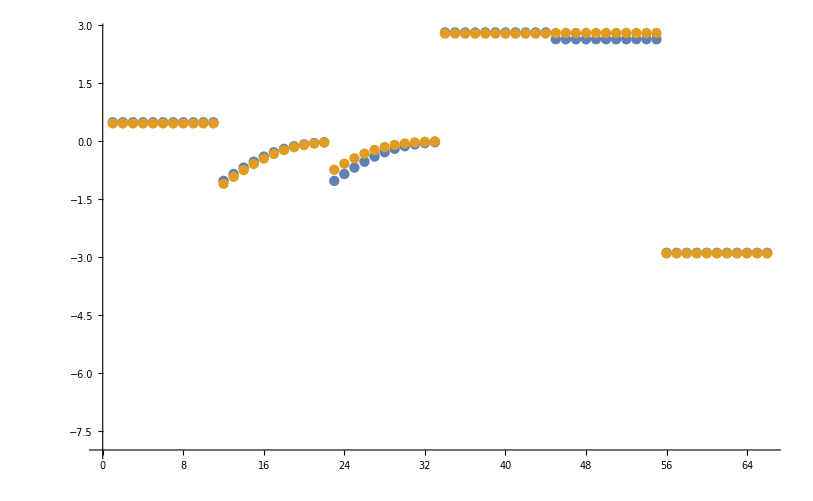

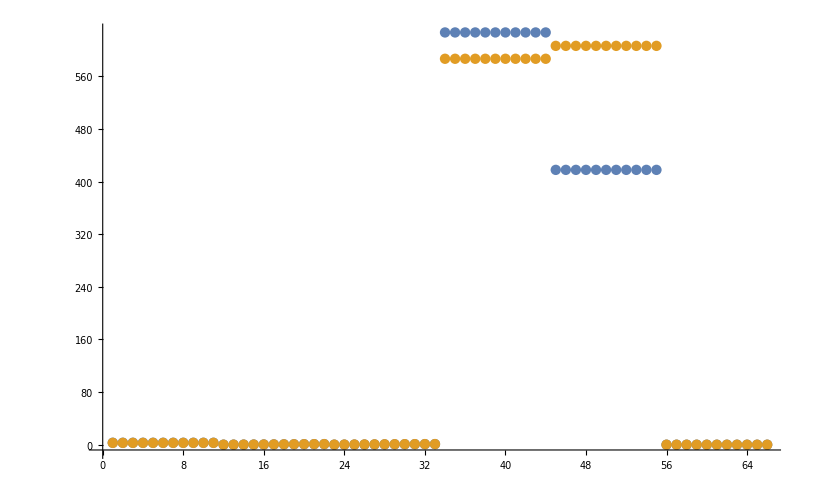

```mathematica
dataSetI=3;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

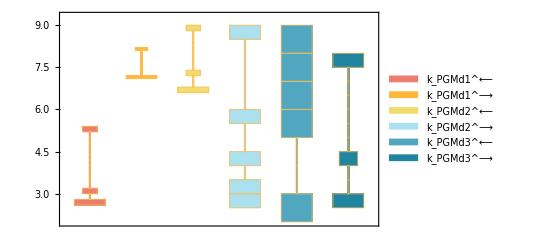

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;5,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

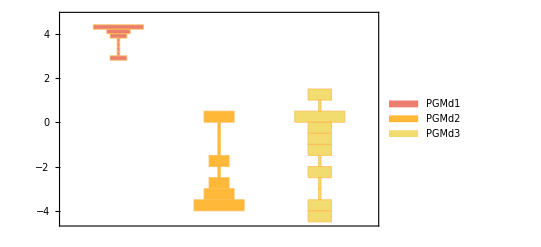

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

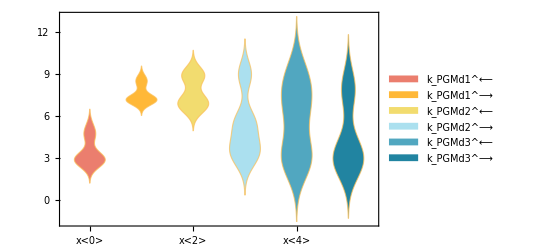

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

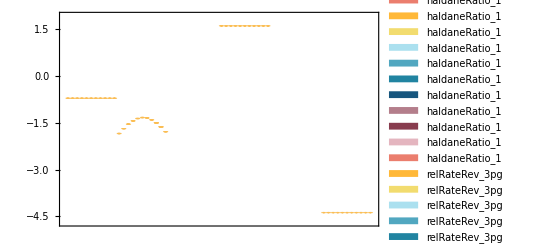

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

-5.65331 | -1.35349 | -1.42935 | -2.09647 | 3.55581 | 0.395924

#### Parameter Cluster Plots (Optional)

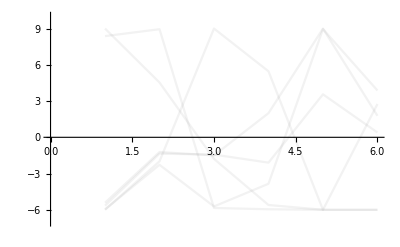

{-Graphics-}

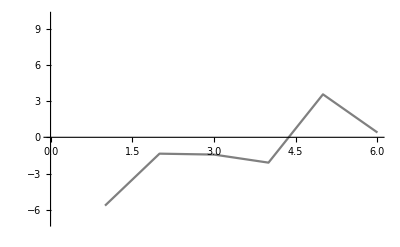

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0002 | 0.000240823 | 20.4114
0.00019 | 0.000089181 | 53.0626

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
626.718 | 586.699 | 6.3855
417.812 | 606.333 | 45.1211

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.9815 | 2.79118 | 6.3834

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.9815 | 2.79118 | 6.3834

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

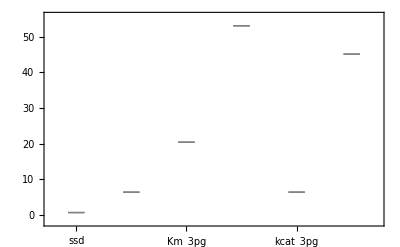

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit =10;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pgmd already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmd\rateconst_labels_pgmd.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmd\S_pgmd.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PGMd[c],E_PGMd[c]&2pg,2pg[c],3pg[c],E_PGMd[c]&3pg}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmd\species_pgmd.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PGMd1: 2pg[c] + E_PGMd[c] <=> E_PGMd[c]&2pg,PGMd2: E_PGMd[c]&3pg <=> 3pg[c] + E_PGMd[c],PGMd3: E_PGMd[c]&2pg <=> E_PGMd[c]&3pg}

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmd\reactions_pgmd.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PGMd[c],E_PGMd[c]&2pg,E_PGMd[c]&3pg}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PGMd1_rev*k_PGMd2_fwd*param_PGMd_total) - k_PGMd2_fwd*k_PGMd3_fwd*param_PGMd_total - k_PGMd1_rev*k_PGMd3_rev*param_PGMd_total)/(2pg(c)*k_PGMd1_fwd*k_PGMd2_fwd + k_PGMd1_rev*k_PGMd2_fwd + 3pg(c)*k_PGMd1_rev*k_PGMd2_rev + 2pg(c)*k_PGMd1_fwd*k_PGMd3_fwd + k_PGMd2_fwd*k_PGMd3_fwd + 3pg(c)*k_PGMd2_rev*k_PGMd3_fwd + 2pg(c)*k_PGMd1_fwd*k_PGMd3_rev + k_PGMd1_rev*k_PGMd3_rev + 3pg(c)*k_PGMd2_rev*k_PGMd3_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmd\rateconst_clusters_pgmd.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
```

```mathematica
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pgmd\rateLaw_pgmd.txt